# Dispersion and Electric Field Code

## Compact Code for computation

## Parameters Choices

```mathematica
Clear["Global`*"]
```

Constants

```mathematica
Clear[c, μ,ϵ,dU, m ,ω, nm,KzBranchesR,KzBranchesI,KzBranchesARP]
```

```mathematica
c = 299792458(*m/s*); 
μ[0]= 4π*10^-7(* N/A^2*);
ϵ[0]= 1/(μ[0] c^2)(*F/m  A^2 s^4 kg^-1  C^2 N^-1 m^-2  *);
m[e]= 9.10938356*10^-31(*in kilograms*);
ω[p]= 2.104*10^15*2*π(*rad/sec*);
nm = 10^-9;
ϵ∞[GaAs] = 13.13;
```

Transformations

```mathematica
dU[n_] = ω[p]/c*n*10^-9 (*nm to unitless*);
```

Beware KzBranches[1] gives two, kz[1] kz[1]

```mathematica
KzBranchesR[n_]:=KzBranchesR[n]=Join[{kz[1]-> -I √(kx^2-ϵ[1] Ω^2) }, Table[kz[j]->√(-kx^2+ϵ[j] Ω^2),{j,2,n-1}],{kz[n]->  I √(kx^2-ϵ[n] Ω^2)}]
```

```mathematica
KzBranchesRN[n_]:=KzBranchesRN[n]=Join[{kz[1]-> -I √(kx^2-ϵ[1] Ω^2) }, Table[kz[j]->-√(-kx^2+ϵ[j] Ω^2),{j,2,n-1}],{kz[n]->  I √(kx^2-ϵ[n] Ω^2)}]
```

```mathematica
KzBranchesI[n_]:=KzBranchesI[n]=Join[{kz[1]-> -I √(kx^2-ϵ[1] Ω^2) }, Table[kz[j]->I √(kx^2-ϵ[j] Ω^2),{j,2,n-1}],{kz[n]->  I √(kx^2-ϵ[n] Ω^2)}]
```

```mathematica
KzBranchesIN[n_]:=KzBranchesIN[n]=Join[{kz[1]-> -I √(kx^2-ϵ[1] Ω^2) }, Table[kz[j]->-I √(kx^2-ϵ[j] Ω^2),{j,2,n-1}],{kz[n]->  I √(kx^2-ϵ[n] Ω^2)}]
```

```mathematica
KzBranchesARP[n_] := 
KzBranchesARP[n]=KzBranchesARP[n] = Table[kz[j]->√(ϵ[j] Ω^2-kx^2),{j,1,n}]
```

```mathematica
KzBranchesGW[n_, j_]:=KzBranchesGW[n, j] = KzBranchesI[n]/.{Rule[kz[j],_]:>Rule[kz[j],√(ϵ[j] Ω^2-kx^2)],Rule[kz[n],_]:> Rule[kz[n],kz[1]] }
```

```mathematica
KzBranchesRR[n_]:= KzBranchesRR[n] = Join[{kz[1]-> √(-kx^2+ϵ[1] Ω^2) }, Table[kz[j]->I √(kx^2-ϵ[j] Ω^2),{j,2,n}]]
```

Parameters

```mathematica
Clear[parameterChoices0]
```

```mathematica
parameterChoices0 = {ϵ[glass]->1.55^2,ϵ[air]->1.00059, ϵ[goldDrudeND]->1 -1/Ω^2, ϵ[TiO2]->5.1,ϵ[goldDrude]->1-1/(Ω^2+I Γ Ω) , ϵ[sf11]-> 3.1852, ϵ[pdot]-> 2.27949604, ϵ[teflon]->1.33^2};
```

```mathematica
parameterChoicesR = {kx -> √ϵ[1] Ω Sin[θ] , Ω -> (2π c)/(λ ω[p])}; (*angle in degrees*)
```

```mathematica
MIMϵs[n_]:=Flatten@Join[Table[{ϵ[j]->ϵ[air], ϵ[j+1]->ϵ[goldDrudeND], ϵ[j+2]->ϵ[TiO2], ϵ[j+3]->ϵ[goldDrudeND]},{j, Table[1 +4j, {j, 0,n-1}]}],{ϵ[1+4n]-> ϵ[air]}]
```

```mathematica
MIMϵDs[n_]:= Flatten@Join[Table[{ϵ[j]->ϵ[air], ϵ[j+1]->ϵ[goldDrude], ϵ[j+2]->ϵ[TiO2], ϵ[j+3]->ϵ[goldDrude]},{j, Table[1 +4j, {j, 0,n-1}]}],{ϵ[1+4n]-> ϵ[air]}]
```

```mathematica
MIMds[n_,  d2_, d3_, d4_, d5_]:=Flatten@Table[{d[j]->dU[d2], d[j+1]->dU[d3], d[j+2]->dU[d4], d[j+3]->dU[d5]},{j, Table[2 +4j, {j, 0,n-1}]}]/. Rule[d[Evaluate[1+4n]], _]:> Rule[d[Evaluate[1+4(n)]], 0]
```

```mathematica
MIMzs[interfaces_]:= Flatten@Join[{z[1]-> 0},Table[z[j]-> d[j]+z[j-1],{j, 2, interfaces}]]
```

```mathematica
parametersMIMs[n_, d2_, d3_, d4_, d5_]:= Join[MIMϵs[n], MIMds[n, d2,d3,d4, d5], MIMzs[4n], KzBranchesI[5+ 4(n-1)], parameterChoices0]
```

```mathematica
parametersMIMsD[n_, d2_, d3_, d4_, d5_, damping_]:= Join[MIMϵDs[n], MIMds[n, d2,d3,d4, d5], MIMzs[4n], KzBranchesI[5+ 4(n-1)], {Γ ->damping}, parameterChoices0]
```

Code for parameter Choices for reflectance.

```mathematica
MIMϵsDR[n_, ϵprism_]:=Flatten@Join[{ϵ[1]->ϵprism},Table[{ϵ[j]->ϵ[air], ϵ[j+1]->ϵ[goldDrude], ϵ[j+2]->ϵ[TiO2], ϵ[j+3]->ϵ[goldDrude]},{j, Table[2 +4j, {j, 0,n-1}]}],{ϵ[2+4n]-> ϵ[air]}]
```

```mathematica
MIMdsR[n_, d2_, d3_, d4_, d5_]:=Flatten@Join[Table[{d[j]->dU[d2], d[j+1]->dU[d3], d[j+2]->dU[d4], d[j+3]->dU[d5]},{j, Table[2 +4j, {j, 0,n-1}]}],{d[2+4n]->0 }];
```

```mathematica
MIMzs[interfaces_]:= Flatten@Join[{z[1]-> 0},Table[z[j]-> d[j]+z[j-1],{j, 2, interfaces}]]
```

```mathematica
parametersMIMsRWR[n_,ϵprism_, d2_, d3_, d4_, d5_, damping_]:= 
Join[MIMϵsDR[n,ϵprism], MIMdsR[n, d2,d3,d4, d5], 
     MIMzs[4n+1], KzBranchesRR[6+ 4(n-1)], 
     {Γ ->damping}, parameterChoices0]
```

```mathematica
parametersMIMsDR[n_,ϵprism_, d2_, d3_, d4_, d5_, damping_]:= 
Join[MIMϵsDR[n,ϵprism], MIMdsR[n, d2,d3,d4, d5], 
     MIMzs[4n+1], KzBranchesRR[6+ 4(n-1)], 
     {Γ ->damping}, parameterChoices0, parameterChoicesR]
```

## Transfer Matrix Code

```mathematica
Clear[MatrixA, InverseMatrixA, MatrixC,Z,MatrixP,MatrixB,PdotB,MatrixM,MatrixInvAMA]
```

```mathematica
Z[n_]:=Z[n]= kz[n]/ϵ[n]
```

```mathematica
InverseMatrixA[n_]:=InverseMatrixA[n]={{E^(-ⅈ kz[n] z[n]),0},
									    {0,E^(ⅈ kz[n] z[n])}}
```

```mathematica
MatrixA[n_]:=MatrixA[n]={{E^(I kz[n]z[n]),0},
						{0,E^(-I kz[n]z[n])}}
```

```mathematica
MatrixB[n_]:=MatrixB[n]={{(Z[n]+Z[n+1])/(2Z[n]), (Z[n]-Z[n+1])/(2Z[n])},
						{(Z[n]-Z[n+1])/(2Z[n]),(Z[n]+Z[n+1])/(2Z[n])}}
```

```mathematica
MatrixC[n_]:=MatrixC[n]={{E^(-I kz[n+1]z[n]),0},
						{0,E^(I kz[n+1]z[n])}}
```

```mathematica
MatrixP[n_]:=P[n]={{E^(I kz[n]d[n]),0},
				    {0,E^(-I kz[n]d[n])}}
```

```mathematica
PdotB [n_]:=PdotB[n]=MatrixP[n].MatrixB[n-1]
```

```mathematica
MatrixM[n_]:=MatrixM[n]=Fold[Dot,PdotB[n],Reverse@Array[PdotB,n-2,2] ] (*this is the matrix you need to compute the determinant and reflectance, this is matrix ℳ of the pdf*)
```

```mathematica
factorM[n_]:=2^n Product[ kz[j]ϵ[j+1], {j, 1, n}]
```

```mathematica
MatrixMC[n_]:= MatrixM[n]*factorM[n-1]
```

```mathematica
MatrixInvAMA[n_]:=MatrixM[n]=Dot[InverseMatrixA[n], MatrixM[n], MatrixA[1]]
```

```mathematica
TransferF[n_]:=TransferF[n]=MatrixC[n].MatrixB[n].MatrixA[n]
```

```mathematica
TransferFF[n_]:=TransferFF[n] = Fold[Dot,TransferF[n], Reverse@Array[TransferF,n-1,1]]
```

## Electric Fields Code

```mathematica
fieldsList::usage = "fieldsList[# of interfaces, parameterChoices] will return a list of fuctions dependent of z, which describe the electric fields inside the device we decide to make based on the parameterChoices we give it. We assume that the first layer as an amplitud of 1, to construct the functions we apply linear transformations which we call transfer matrices which relate the Electric Field amplitudes at each interface, then apply a final linear transformation which are the incoming and outgoing exponential functions of the E-fields of the layer we desire to plot.";
```

```mathematica
fieldsList[n_, parameterChoices_]:=Reverse@Flatten[Select[{ 
							Power[Norm[{Exp[I kz[n+1] z],0}.TransferFF[n].{1,0}//. parameterChoices],2](*Semi-Infinite last layer field*),
							Reverse@Table[Power[Norm[{Exp[I kz[j+1] z], Exp[- I kz[j+1] z]}.TransferFF[j].{1,0}//.parameterChoices],2],{j,1,n-1}],
							 {Power[Norm[Exp[I kz[1]z]//. parameterChoices],2]} (*Semi-Infinite first layer field*)}, UnsameQ[#, {}]&]]
```

```mathematica
plotEfields[n_, parameterChoices_]:=
Module[
	{interfaces = n, 
	parameterChoicesFields = parameterChoices, 
	linesList, 
	EfuncList, 
	piecewiseList}, 

linesList =  { Evaluate[Table[{z[j], {Orange,Thickness[0.002]}}, {j, 1, interfaces}]//.parameterChoicesFields], None}
(*we have n interfaces,so then we must have z[1], z[2],..., z[n]*);
EfuncList = fieldsList[interfaces, parameterChoicesFields];
piecewiseList =
Join[{{EfuncList[[1]], z<0}(*first*)},Table[{EfuncList[[j]], ((z[j-1]<z< z[j])//.parameterChoicesFields)}, {j,2,n}], {{EfuncList[[n+1]], Evaluate[z>z[n]//.parameterChoicesFields]}} ];
Plot[Piecewise[piecewiseList], {z, -5,( z[n]//.parameterChoicesFields)+5},PlotRange->All, Frame->True, Axes-> False, GridLines-> linesList]
]
```

## E-fields for Infinite Super Lattice Structure

```mathematica
∞SLSfieldsListfieldsList::usage = "∞SLSfieldsListfieldsList[# of interfaces, parameterChoices∞SLS_, ∞SLSdisp_, qL_] will return a list of fuctions dependent of z, which describe the electric fields inside the infinite superLattice structure we decide to make based on the parameterChoices we give it. Before hand we need to define the dispersion relation for that periodic structure, so that we can use it to make the field amplitudes of the first layer, then use transfer matrices to find the field amplitudes of the rest of the layers. Then apply a final linear transformation which are the incoming and outgoing exponential functions of the E-fields of the layer we desire to plot. Also we asume that we have picked kx, Ω and that they are included inside the paramater Choices.";
∞SLSfieldsListfieldsList[n_, parameterChoices∞SLS_, ∞SLSdisp_, qL_]:=Reverse@Flatten[Select[{ 
							Power[Norm[{Exp[I kz[n+1] z],Exp[-I kz[n+1] z]}.TransferFF[n].{-∞SLSdisp[[1,2]],∞SLSdisp[[1,1]] - ⅇ^(I qL)}//. parameterChoices∞SLS],2](*Semi-Infinite last layer field*),
							Reverse@Table[Power[Norm[{Exp[I kz[j+1] z], Exp[- I kz[j+1] z]}.TransferFF[j].{-∞SLSdisp[[1,2]],∞SLSdisp[[1,1]] - ⅇ^(I qL)}//.parameterChoices∞SLS],2],{j,1,n-1}],
							 {Power[Norm[{Exp[I kz[1]z], Exp[-I kz[1]z]}.{-∞SLSdisp[[1,2]],∞SLSdisp[[1,1]] - ⅇ^(I qL)} //. parameterChoices∞SLS],2]} (*Semi-Infinite first layer field*)}, UnsameQ[#, {}]&]]
```

```mathematica
plotEfields∞SLS[n_, parameterChoices∞SLS_,∞SLSdisp_, qL_]:=
Module[
	{interfaces = n, 
	parameterChoicesFields = parameterChoices∞SLS, 
	linesList, 
	EfuncList, 
	piecewiseList}, 

linesList =  {Join [ Evaluate[Table[{z[j], {Orange,Thickness[0.002]}}, {j, 1, interfaces+1}]], {{-d[n+1], {Orange,Thickness[0.002]}}}]//.parameterChoices∞SLS, None}
(*we have n interfaces,so then we must have z[1], z[2],..., z[n]*);
EfuncList = ∞SLSfieldsListfieldsList[interfaces, parameterChoicesFields, ∞SLSdisp, qL];
piecewiseList =
Join[{{EfuncList[[1]],Evaluate[ -d[n+1]<z<0]//.parameterChoicesFields}(*first*)},Table[{EfuncList[[j]], ((z[j-1]<z< z[j])//.parameterChoicesFields)}, {j,2,n}], {{EfuncList[[n+1]], Evaluate[z[n+1]>z>z[n]//.parameterChoicesFields]}} ];
Plot[Piecewise[piecewiseList], {z,-(d[n+1]//.parameterChoicesFields),(z[n+1]//.parameterChoicesFields)},PlotRange->All, Frame->True,FrameLabel->{"z (unitless)", "|E|^2"} ,Axes-> False, GridLines-> linesList]
]
```

```mathematica
Clear[plot∞SLS]
plot∞SLS[n_, parameterChoices_, kx0_, Ω0_, qL_] :=Module[
(*We make the dispersion relation*)
{interfaces = n, 
∞SLSdisp = MatrixM[n+1]//.parameterChoices,
parameterChoicesFields = Join[parameterChoices, {kx->kx0}], 
 root, plotDisp,plotDispPoint, plotEfields},
root = FindRoot[((∞SLSdisp[[1,1]] + ∞SLSdisp[[2,2]])//.{kx->kx0})/2 - Cos[qL]==0, {Ω, Ω0}];
parameterChoicesFields = Join[parameterChoicesFields, root];
plotDisp = ContourPlot[(∞SLSdisp[[1,1]] + ∞SLSdisp[[2,2]])/2 ==Cos[qL], {kx, 0,2},{Ω, 0,1.3},ContourStyle->Orange, MaxRecursion->4, FrameLabel->{"Kx","Ω"}];
plotDispPoint= Show[plotDisp, Graphics[Point[{kx,Ω}//.parameterChoicesFields]]];
plotEfields = plotEfields∞SLS[n, parameterChoicesFields, ∞SLSdisp, qL];
GraphicsRow[{plotDispPoint, plotEfields}]
]
```

## Recursive Root Finding

```mathematica
findRootDisp[disp_,Ω0_, kx0_]:= FindRoot[(disp/.kx->kx0)==0, {Ω, Ω0}]
```

```mathematica
recursiveRootFinding[disp_, Ω0_, kx0_, step_, nPoints_]:=
Thread[
{Table[kx0+stepVar, {stepVar, 0, step*nPoints,step}],
Delete[FoldList[Ω/.Chop@Flatten@findRootDisp[disp,#1(*Ω*), #2 (*kx*)]&, Ω0 (*inital Guess, removed in code*), Table[kx0+stepvar, {stepvar, 0,step*nPoints ,step}](*kx values*)],1]}
]
```

```mathematica
testPoint[disp_, list_]:= Table[disp/.{kx-> list[[j, 1]],Ω-> list[[j, 2]]}, {j, 1, Length@list}]
```

## Visible Region Code

```mathematica
λtoΩ[λ_]:= (2 π c)/(λ ω[p]);
```

```mathematica
λnmtoΩ[λ_]:= (2 π c)/(nm*ω[p]*λ);
```

```mathematica
Ωtoλ[Ω_]:=(2 π c)/(Ω ω[p]);
```

```mathematica
Ωtoλnm[Ω_]:=(2 π c)/(Ω ω[p]*nm);
```

```mathematica
kxfunc[λ_(*nm*),θ_, ϵ_]:=λnmtoΩ[λ]*Sin[(π θ)/180] √ϵ/.parameterChoices0
```

```mathematica
θcriticaln[np_, n1_]:= 180/π ArcSin[(n1/np)/.parameterChoices0]
```

```mathematica
θcriticalϵ[ϵp_, ϵ1_]:= 180/π ArcSin[((√ϵ1)/(√ϵp))/.parameterChoices0]
```

```mathematica
TIRvisiblePoints[ϵp_, ϵ1_]:= 
Module[{ϵprism = ϵp//.parameterChoices0, 
	    ϵlayer1= ϵ1//.parameterChoices0, 
	    λa = 488 (*nm*), λz = 640(*nm*),θc, θz = 63, pointList}(*we assume that the critical angle does not exceed *),
		θc = θcriticalϵ[ϵprism, ϵlayer1];
		pointList = {{kx[ λz,θc, ϵprism], λnmtoΩ[λz]},{kx[ λz,θz, ϵprism], λnmtoΩ[λz]},
				     {kx[ λa,θz, ϵprism], λnmtoΩ[λa]},{kx[ λa,θc, ϵprism], λnmtoΩ[λa]}};
		Graphics[{RGBColor[0.4,0.9,1],Opacity[0.5],Polygon[pointList]}]
]
```

## Infinite Super Lattice Code, Shaded in, plots

```mathematica
parameterChoices=Join[KzBranchesARP[5],{ϵ[1]-> ϵ[air],ϵ[2]->ϵ[goldDrudeND],ϵ[3]->ϵ[TiO2],ϵ[4]->ϵ[goldDrudeND], ϵ[5]->ϵ[air], d[2]-> dU[35], d[3]->dU[50],d[4]->dU[35],d[5]->dU[50]}, parameterChoices0]
```

```mathematica
Clear[∞MIM]
```

```mathematica
∞MIM = MatrixM[5]//.parameterChoices;
```

```mathematica
∞MIM/.{kx->1, Ω->0.5}
```

{{-14.5112-1.2946×10^-15 ⅈ,-5.02346-4.30371×10^-16 ⅈ},{228.748+0. ⅈ,79.1185+0. ⅈ}}

```mathematica
∞SLSdisp =ContourPlot[{(∞MIM[[1,1]]+∞MIM[[2,2]])/2==1,(∞MIM[[1,1]]+∞MIM[[2,2]])/2==-1},{kx, 0,2},{Ω,0,1}, PlotPoints->50, MaxRecursion->3, ContourShading->{Gray, Blue}]
```

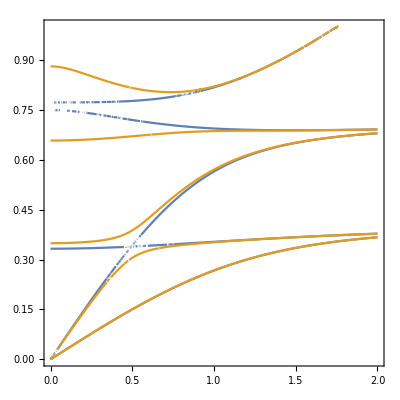

```mathematica
∞SLSshaded= ContourPlot[(∞MIM[[1,1]]+∞MIM[[2,2]])/2,{kx, 0,2},{Ω,0,1},Contours->{-1,1}, ColorFunction->(If[(#1≤0.2 || #1>=1 ), {White, Opacity[1]}, {RGBColor[0.42,0.79,1.], Opacity[0.7]}]&), ContourStyle->None, Method-> {"TransparentPolygonMesh"->True}]
```

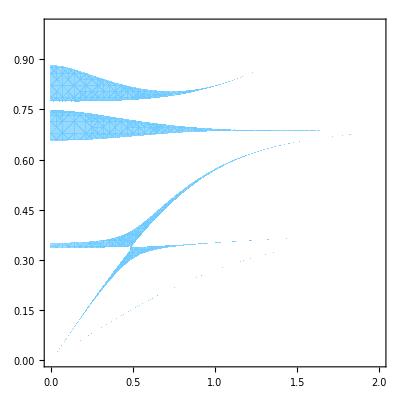

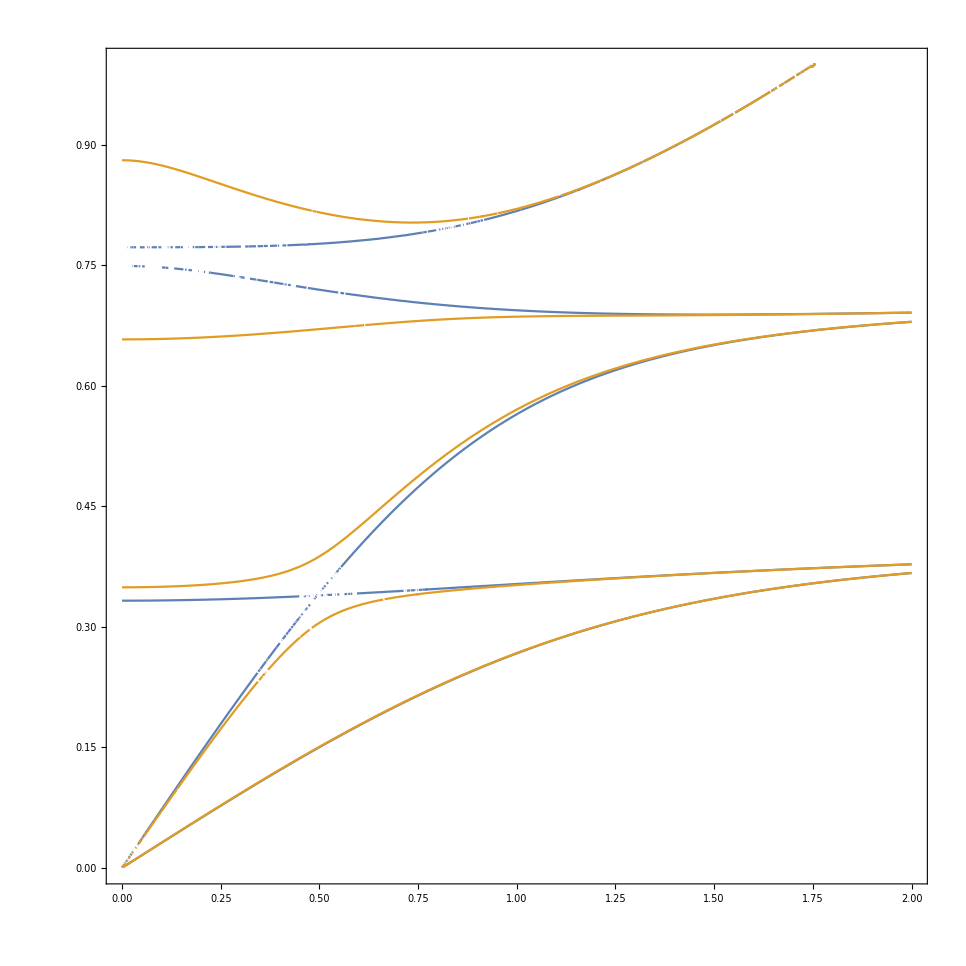
```mathematica
∞SLS = -Graphics-;
```

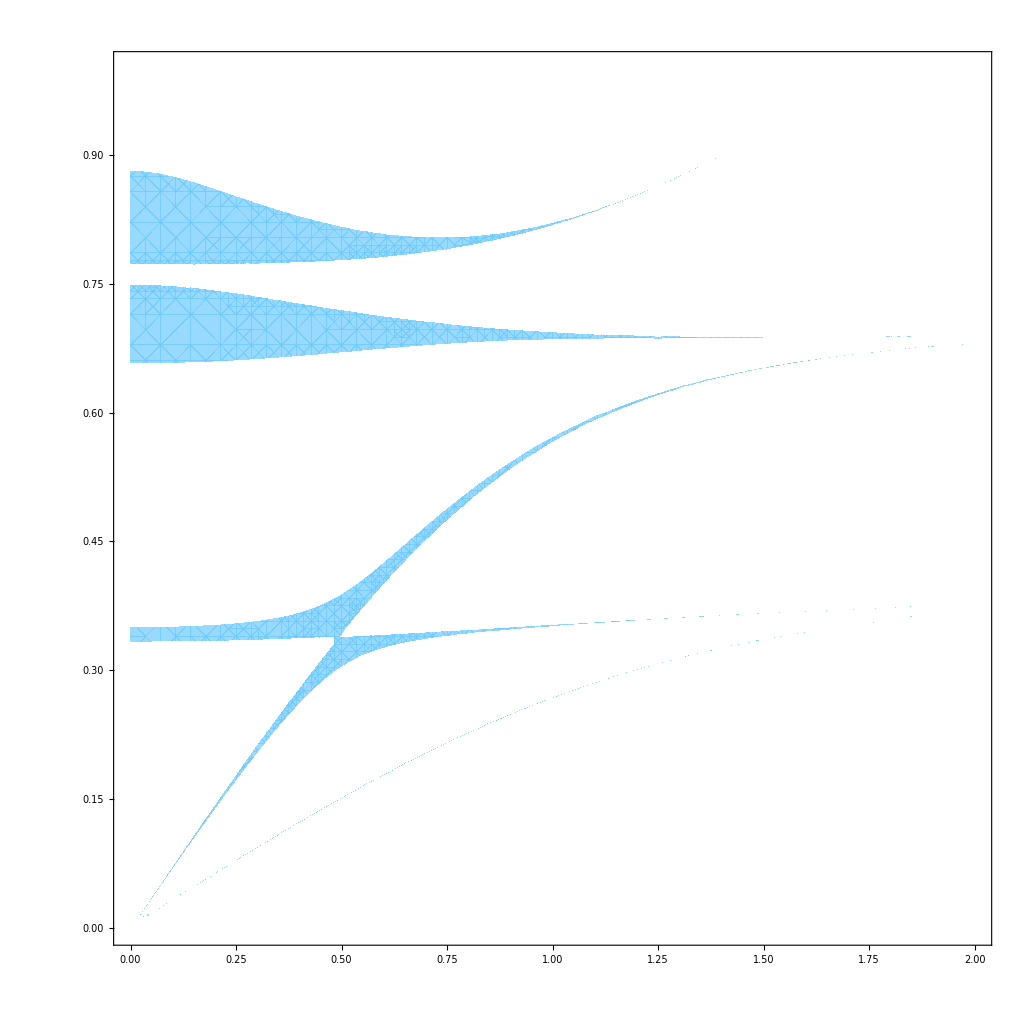
```mathematica
∞SLSshaded=-Graphics-;
```

## ATR Scan \ Reflectance

```mathematica
reflectance[disp_] := Abs[(disp[[2,1]]/disp[[2,2]])^2];
```

```mathematica
ATRfuncλθ[reflectance_, parameterChoices_] := reflectance//.parameterChoicesR//.parameterChoices
```

```mathematica
λtoΩ[λ_]:= (2 π c)/(λ ω[p]);
```

```mathematica
λnmtoΩ[λ_]:= (2 π c)/(nm*ω[p]*λ);
```

```mathematica
Ωtoλ[Ω_]:=(2 π c)/(Ω ω[p]);
```

```mathematica
Ωtoλnm[Ω_]:=(2 π c)/(Ω ω[p]*nm);
```

```mathematica
kxΩtoθλ [kx0_, Ω0_, parameterChoices_]:= {θ-> ArcSin[(kx0/(Ω0*√ϵ[1]))//.parameterChoices], λ->((2π)/(Ω0*ω[p])//.parameterChoices)} (*θ is in radians and λ is in m*)
```

## Plot light lines

```mathematica
lightLinePlot[ϵprism_, start_, end_, color_]:= Plot[{kx/(√ϵprism)//.parameterChoices0}, {kx, start, end}, PlotStyle->color]
```

## Plot ATR Scan line constant dielectric value for prism

```mathematica
atrScanline[ϵprism_, θ_, start_, end_, color_]:=Plot[{kx/(Sin[π/180*θ] √ϵprism)//.parameterChoices0}, {kx,start, end}, PlotStyle->color]
```

## Exporting Tips

To Export a Plot, it is helpful to do (jpeg, etc.)

```mathematica
Export["path/name.jpeg", Rasterize[plot, ImageResolution->800], "JPEG"]
```

To Export data you can use CSV

```mathematica
Export["path/name.csv",data, "CSV"]
```

To Export a Mathematica Equation you can use for example after computing MatrixM[17] //.parameters takes a while you can use

```mathematica
Export["path/name.m", equation]
```